```mathematica
fileName = "/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json";
RadioButtonBar[
Dynamic[fileName],
{
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json",
"~/Downloads/optimizerHistory.json"
},Appearance->"Vertical"]
```

| /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json
 | ~/Downloads/optimizerHistory.json

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

```mathematica
runningBest = FoldList[Max,First[#],Rest[#]]&[raw[[All,"maximizeMe"]]];
```

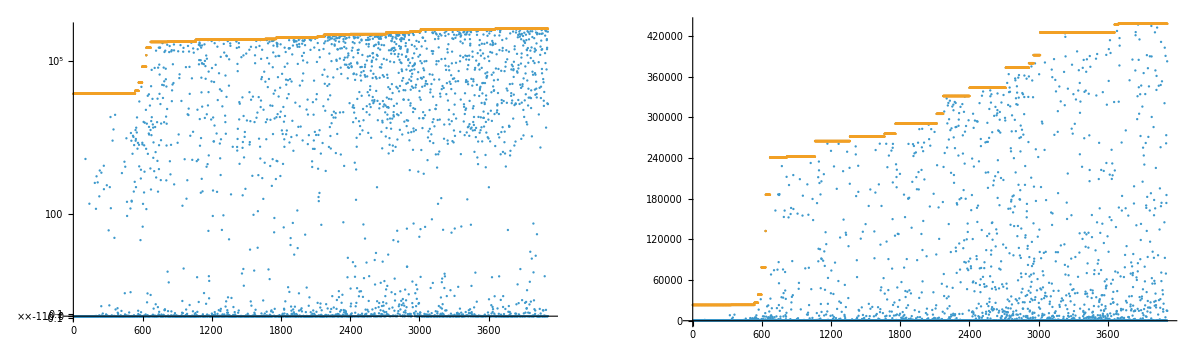

```mathematica
GraphicsGrid[{{
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600,
ScalingFunctions->"SignedLog"
],
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Estimate maximizeMe asymptote

There’s no reason at all to think this is valid

```mathematica
(*runningBest = #["maximizeMe"]&/@raw;*)
```

Calculate

Estimated limits: {390826.,458251.,463000.,467750.,535174.}

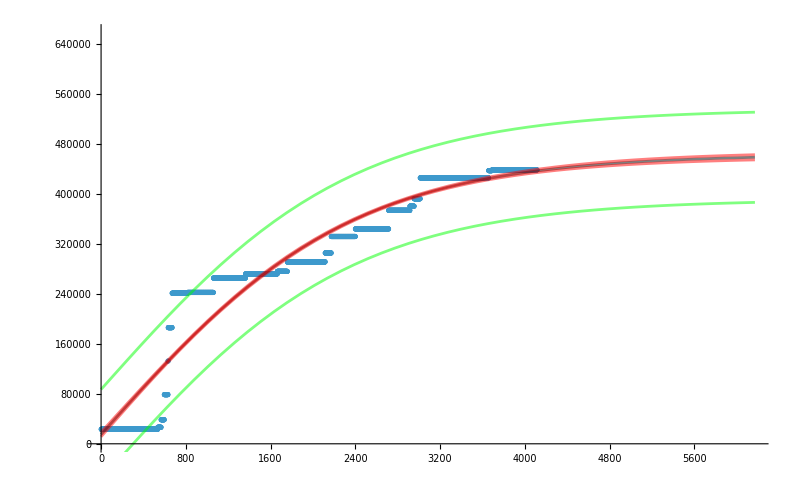

```mathematica
Button["Calculate",

expr = a * Tanh[b ii]+c;
nlm=NonlinearModelFit[
Transpose[{Range[Length[runningBest]],runningBest}],
expr,
{
{a,Max[runningBest]},
{b,1/Length[runningBest]},
{c,Min[runningBest]}
},
ii,
Method->"NMinimize"
];

meanPredictionBands = nlm["MeanPredictionBands"];
singlePredictionBands = nlm["SinglePredictionBands"];
plotMe ={nlm["BestFit"]}~Join~meanPredictionBands~Join~singlePredictionBands;

img = Show[
ListPlot[
Transpose[{Range[Length[runningBest]],runningBest}],
PlotRange->{{0,Length[runningBest]*1.5},{0, Max[runningBest]*1.5}},
ImageSize->800
],

Plot[
plotMe,
{ii,0,Length[runningBest]*1.5},
PlotStyle->{{Opacity[0.5],Black},{Opacity[0.5],Red},{Opacity[0.5],Red},{Opacity[0.5],Green},{Opacity[0.5],Green}},
PlotRange->All
]

];

Print[
"Estimated limits: ",
Sort[
Limit[#,ii->Infinity]&/@plotMe
]
];
Print[img];
]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

L1PhaseSet : -22.0910475464
L2PhaseSet : -36.5285750341
L3PhaseSet : -0.0753215474
Q19851kG : -38.7481392127
Q19871kG : 31.7893463686
B1EkG : 4.5293614078
B2EkG : -6.5338680032
B3EkG : 2.0449578601
Q1EkG : 88.7607628072
Q2EkG : -96.812022497
Q3EkG : 73.1896065543
Q4EkG : 61.7130709988
Q5EkG : -1.3597561163
Q6EkG : -96.5554774578
S1ELkG : 1067.343172951
S2ELkG : -6789.5718338296
S3ELkG : -624.8843999974
S3ERkG : -429.5372744113
S2ERkG : -4291.2883002511
S1ERkG : 445.9640008271
S1EL_xOffset : 0.00011162
S1EL_yOffset : -0.0002328616
S2EL_xOffset : 0.0002850456
S2EL_yOffset : -0.0001852753
S2ER_xOffset : -0.0004922119
S2ER_yOffset : 0.0002586316
S1ER_xOffset : 0.0003449444
S1ER_yOffset : 0.0003138228
PDrive_median_x : 0.0000438703
PDrive_median_y : 0.0000128667
PDrive_median_xp : 0.0001842634
PDrive_median_yp : -2.5475e-6
PDrive_median_energy : 6.041099824687280655e9
PDrive_sigmaSI90_x : 0.0000713909
PDrive_sigmaSI90_y : 0.0000359974
PDrive_sigmaSI90_z : 5.0021e-6
PDrive_sigmaSI90_xp : 0.0003622596
PDrive_sigmaSI90_yp : 0.0000245614
PDrive_sigmaSI90_energy : 6.7992445541355342e7
PDrive_emitSI90_x : 0.00029906
PDrive_emitSI90_y : 0.0000103014
PDrive_norm_emit_x : 0.0000226641
PDrive_norm_emit_y : 6.4475e-6
PDrive_zCentroid : 991.3312669052
PDrive_charge_nC : 1.20264144
PDrive_BMAG_x : 1.858571015
PDrive_BMAG_y : 1.7493326775
PDrive_sliced_BMAG_x : List(15.0604491631,4.8275739931,2.8527450702,2.0180887861,2.5731734278)
PDrive_sliced_BMAG_y : List(1.9728828279,3.1125541434,3.6432618431,2.328526437,1.3311176852)
PWitness_median_x : 0.0000449358
PWitness_median_y : 0.0000115648
PWitness_median_xp : -0.0003965198
PWitness_median_yp : 0.000066554
PWitness_median_energy : 5.879970496507875442e9
PWitness_sigmaSI90_x : 0.0000726116
PWitness_sigmaSI90_y : 0.0000244607
PWitness_sigmaSI90_z : 4.8623e-6
PWitness_sigmaSI90_xp : 0.0001412037
PWitness_sigmaSI90_yp : 0.0000625777
PWitness_sigmaSI90_energy : 7.74148222826636e6
PWitness_emitSI90_x : 0.0000249854
PWitness_emitSI90_y : 0.0000125354
PWitness_norm_emit_x : 0.0000212179
PWitness_norm_emit_y : 7.3894e-6
PWitness_zCentroid : 991.3312997714
PWitness_charge_nC : 0.39816144
PWitness_BMAG_x : 5.2253408345
PWitness_BMAG_y : 1.3066146181
PWitness_sliced_BMAG_x : List(8.7921990631,8.4858109243,8.3678385592,7.7282750723,12.2137249161)
PWitness_sliced_BMAG_y : List(1.2550398586,1.3427242947,1.8126996982,1.7268864397,1.1289733842)
bunchSpacing : 0.0000328662
transverseCentroidOffset : 1.6823e-6
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 2.2e-8
errorTerm_secondaryObjective : 0.0000205198
maximizeMe : 438130.4232528029
inputBeamFilePathSuffix : "/beams/2025-05-13_twobunch_unoptimized_shortSpacing/2025-05-13_twobunch_unoptimized_shortSpacing.h5"
csrTF : False

```mathematica
(*Not tested to be robust... beware!*)
indepVarKeys = Keys[raw[[1]]][[1;;(Position[Keys[raw[[1]]],"PDrive_median_x"][[1,1]]-1)]]
```

{L1PhaseSet,L2PhaseSet,L3PhaseSet,Q19851kG,Q19871kG,B1EkG,B2EkG,B3EkG,Q1EkG,Q2EkG,Q3EkG,Q4EkG,Q5EkG,Q6EkG,S1ELkG,S2ELkG,S3ELkG,S3ERkG,S2ERkG,S1ERkG,S1EL_xOffset,S1EL_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S1ER_xOffset,S1ER_yOffset}

## Plot specific

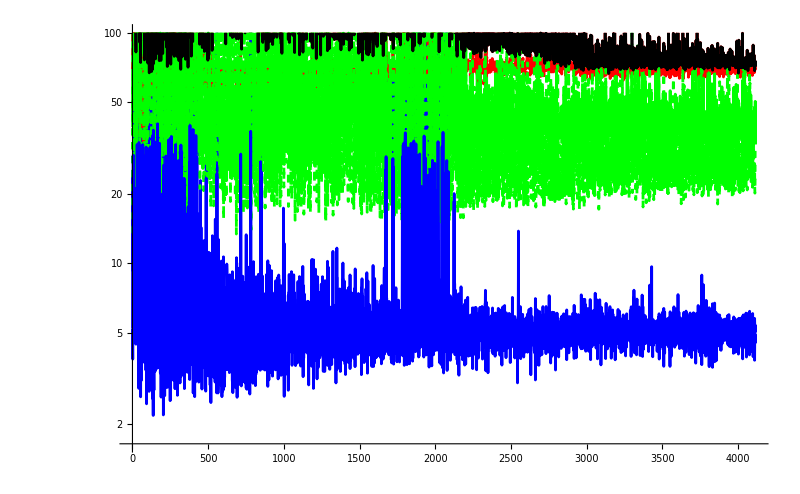

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{All,100}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

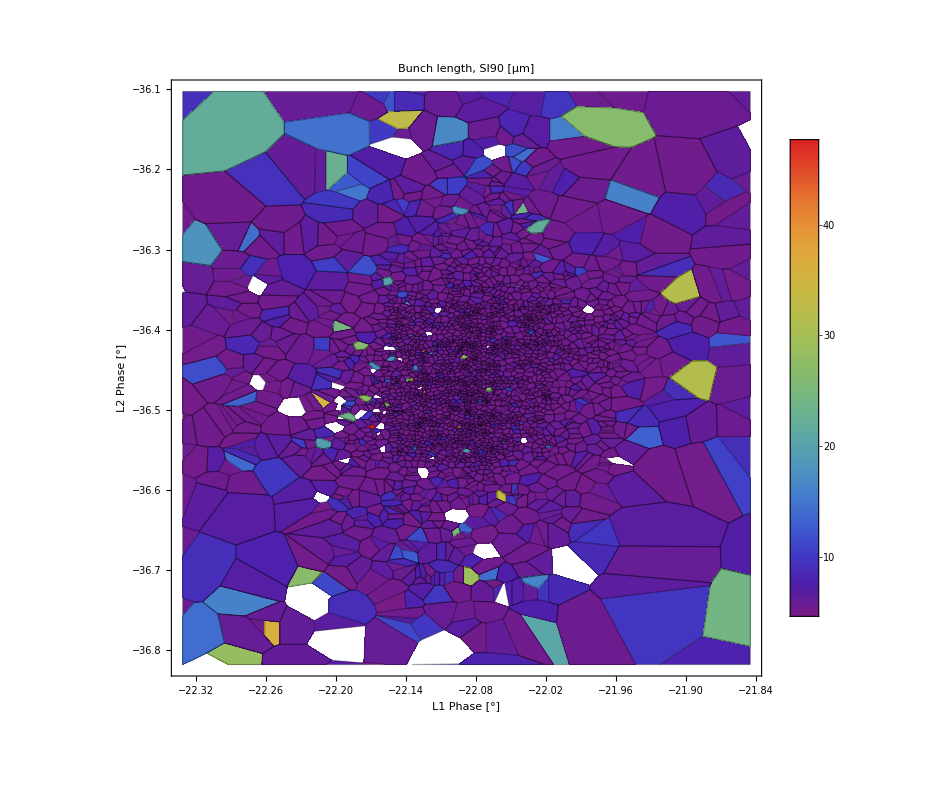

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,
PlotRange->{All,50},
(*PlotRange->{{-35,-21},{-50,-30},{All,50}},*)
Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"Bunch length, SI90 [μm]",LabelStyle->20]
```

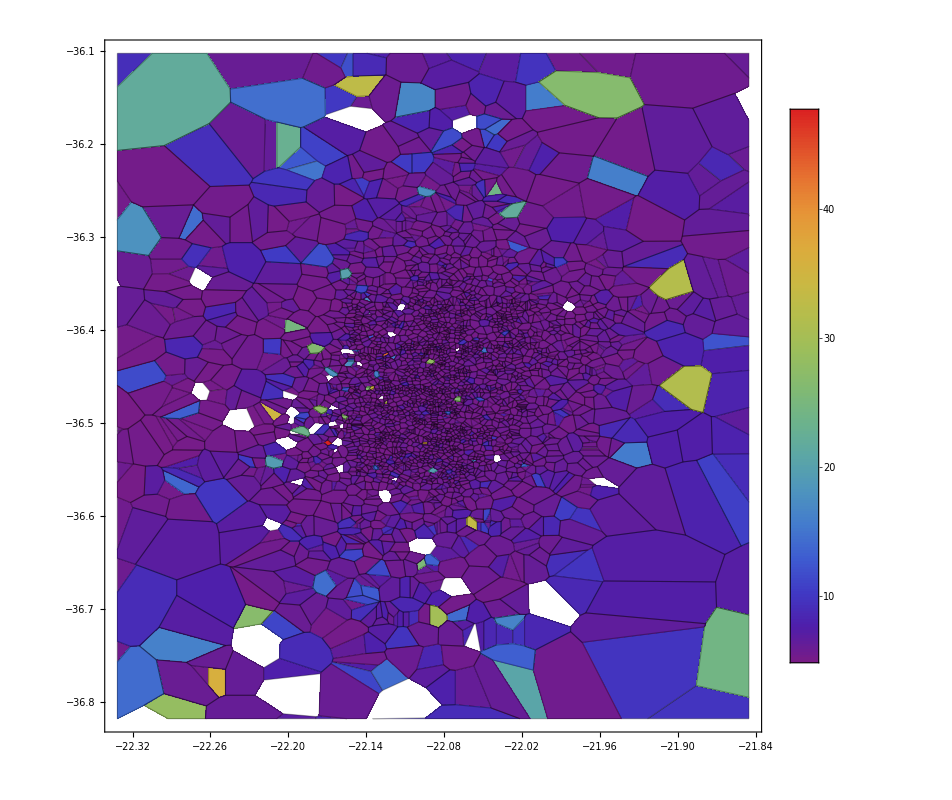

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

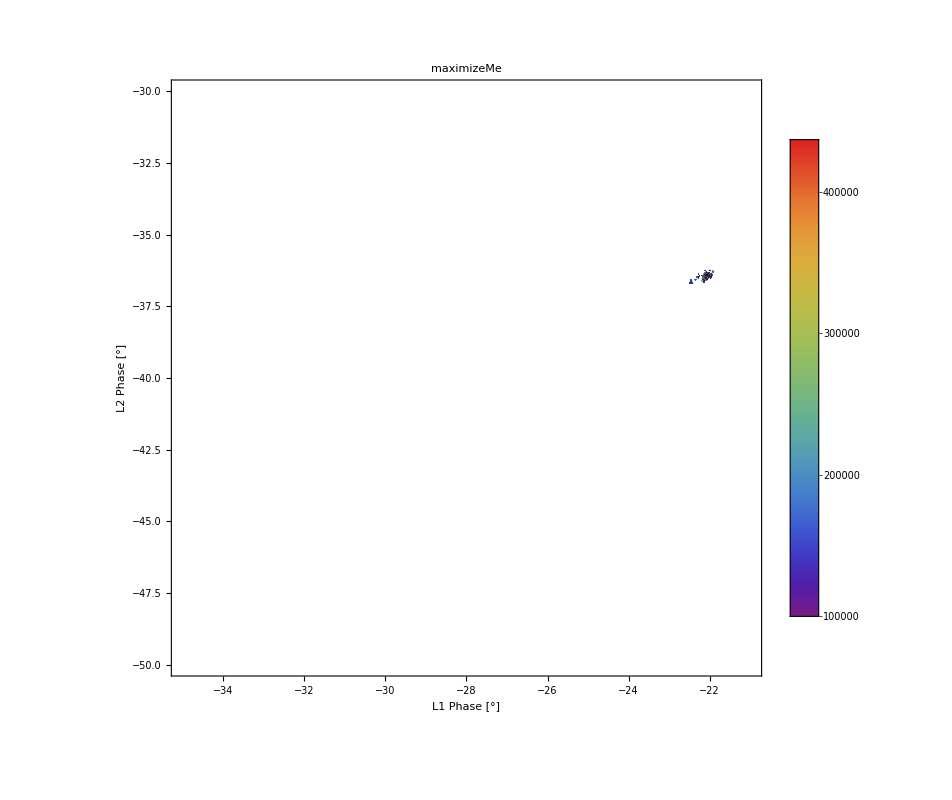

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
#["maximizeMe"]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",
InterpolationOrder->0,
(*PlotRange->{1*^5,All},*)
PlotRange->{{-35,-21},{-50,-30},{1*^5,All}},
Mesh->All,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"maximizeMe",LabelStyle->20]
```

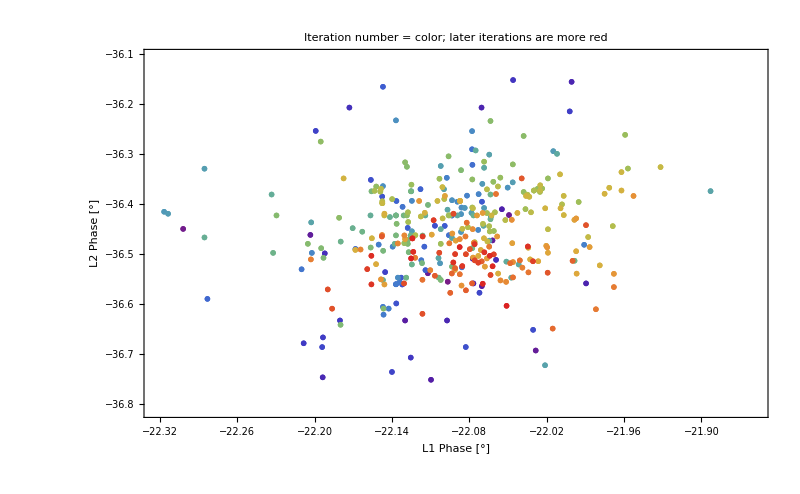

```mathematica
toPlot = {
#["L1PhaseSet"],
#["L2PhaseSet"]
}&/@raw[[1;;-1;;10]];
colors = Table[ColorData["Rainbow"][Rescale[i,{1,Length[toPlot]}]],{i,Length[toPlot]}];

ListPlot[{#}&/@toPlot,
ImageSize->800,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},
LabelStyle->20,
Frame->True,
PlotStyle->colors,
PlotLabel->"Iteration number = color; later iterations are more red",
PlotMarkers->{Graphics[Disk[]],0.01}
]
```

```mathematica
(*Show[
ListContourPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"],
(10^6#["PDrive_sigmaSI90_z"])
}&/@raw,
PlotLegends->Automatic,
ImageSize->800,
SphericalRegion->True,
Contours->{4,4.9,5,5.1,6}
],
ListPointPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"]
}&/@raw
]
]*)
```

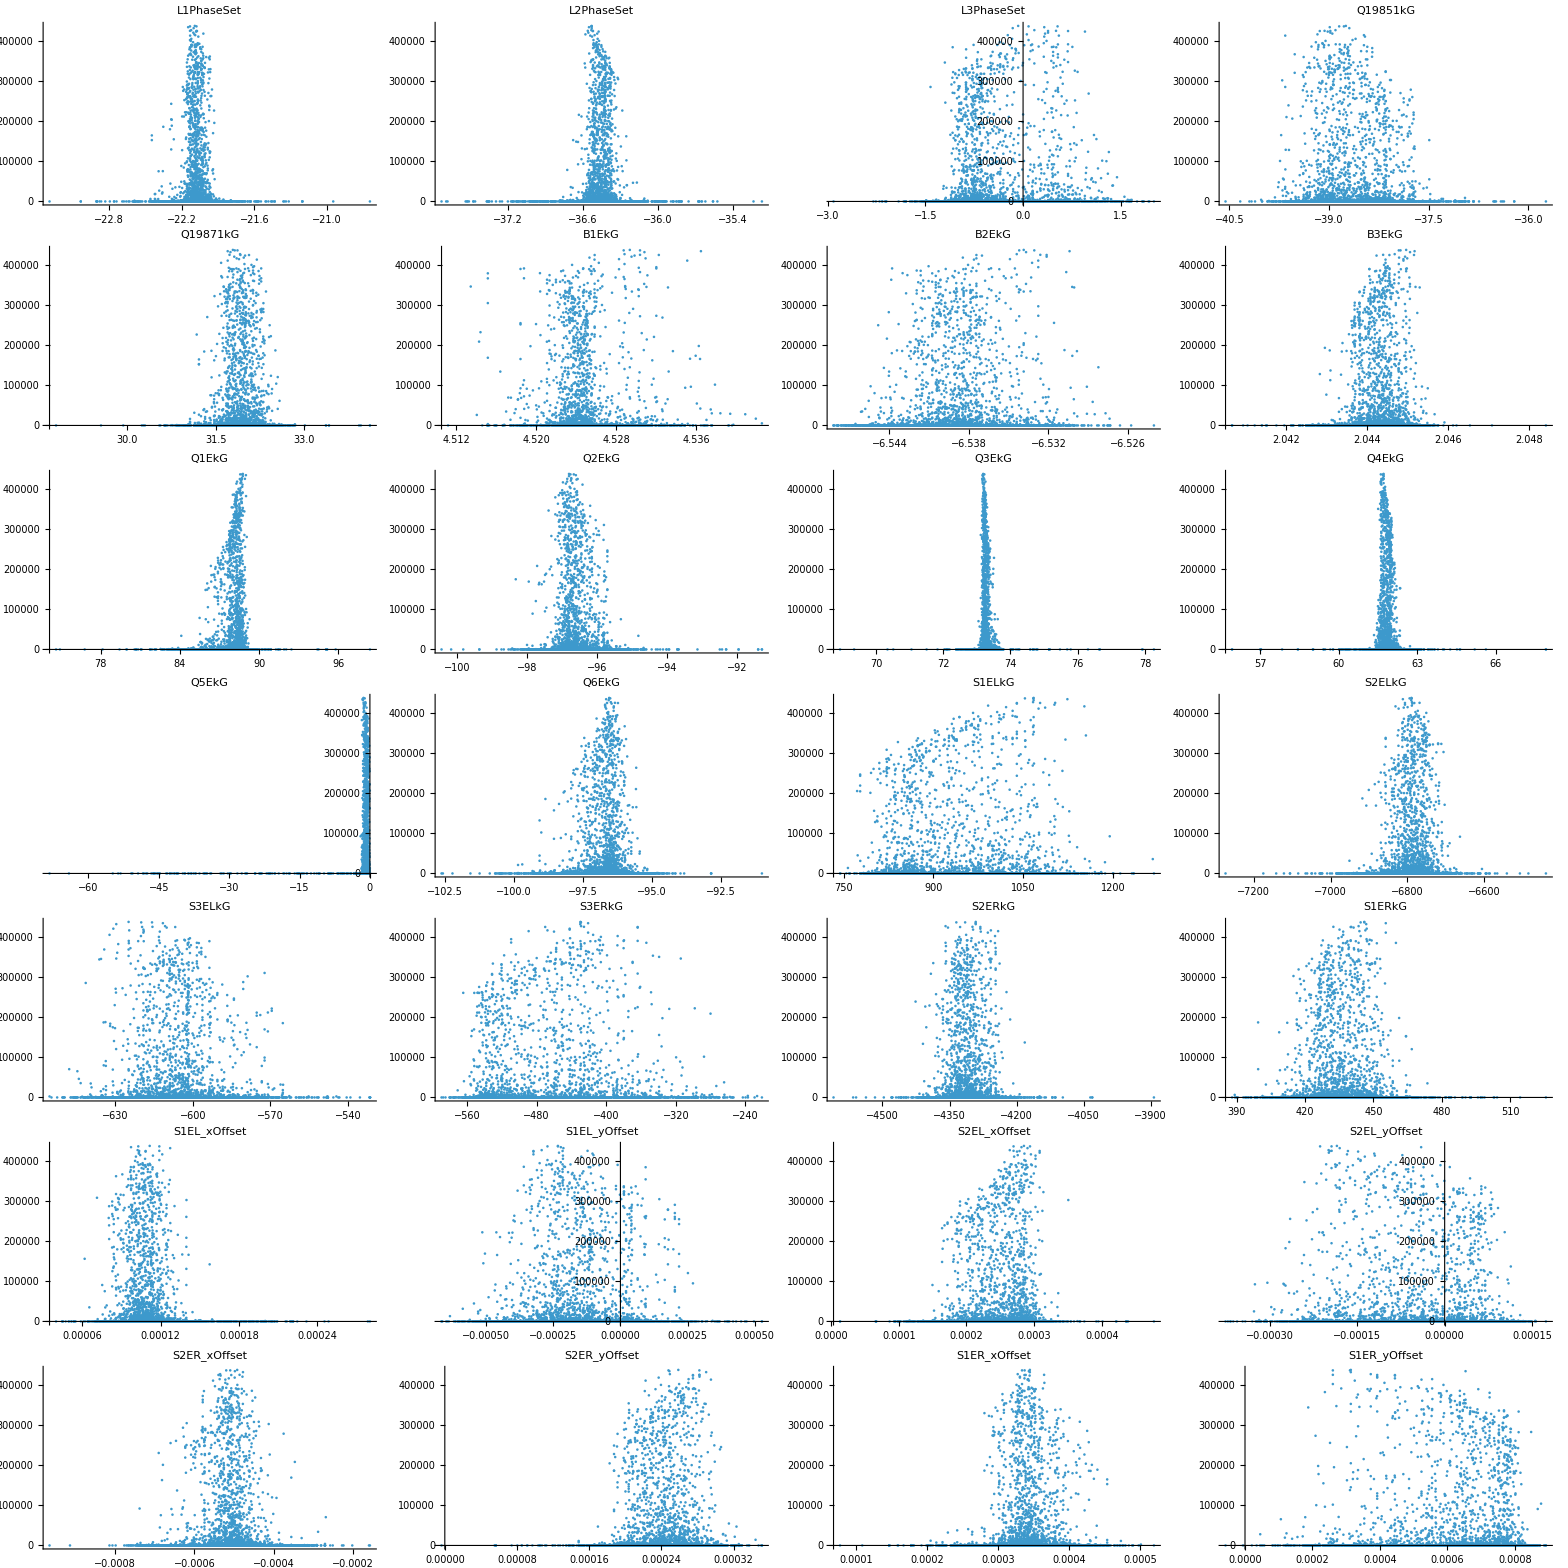

```mathematica
imgArr=ParallelTable[
ListPlot[
{#[key],#["maximizeMe"]}&/@raw,
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All
],
{key,indepVarKeys}
];

displayCols = 4;
Grid[
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
],
Frame->All
]
```

## Plot all

```mathematica
(*This block can get really slow for large numbers of simulations; pare down number of points to plot*)
shotCount = Length[raw[[All,1]]];
indicesToPlot = DeleteDuplicates[Round[Range[1,shotCount,shotCount/1000]]];
```

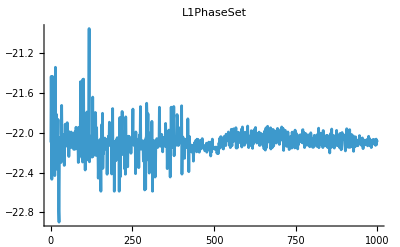
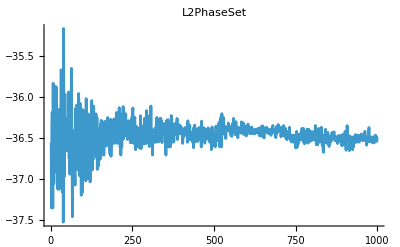
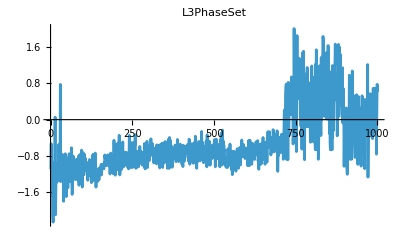
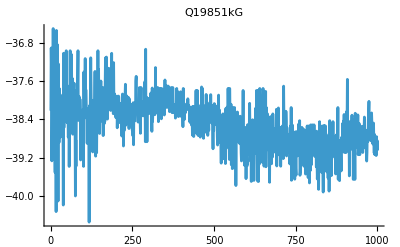
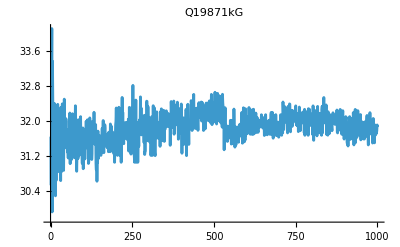
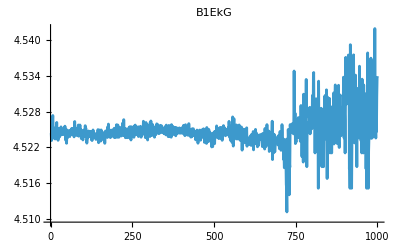
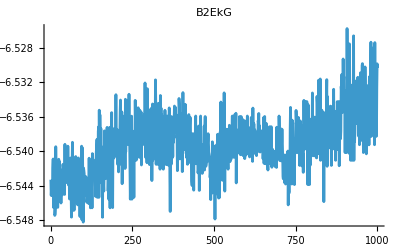
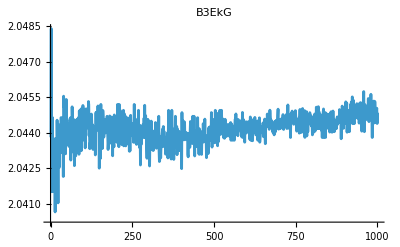
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | 0 | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
raw[[indicesToPlot,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,L3PhaseSet,Q1EkG,Q2EkG,Q3EkG,Q4EkG,Q5EkG,Q6EkG,S1ELkG,S1EL_xOffset,S1EL_yOffset,S1ERkG,S1ER_xOffset,S1ER_yOffset,S2ELkG,S2EL_xOffset,S2EL_yOffset,S2ERkG,S2ER_xOffset,S2ER_yOffset,S3ELkG,S3ERkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | -22.091 | -1.779
L2PhaseSet | -38.6737 | -36.5286 | 2.14513
L3PhaseSet | -1.46329 | -0.0753215 | 1.38797
S1EL_xOffset | 0.000385255 | 0.00011162 | -0.000273635
S1EL_yOffset | -0.000241114 | -0.000232862 | 8.2521×10^-6
S2EL_xOffset | -0.00141787 | 0.000285046 | 0.00170291
S2EL_yOffset | 0.0000111705 | -0.000185275 | -0.000196446
S2ER_xOffset | -0.00223816 | -0.000492212 | 0.00174595
S2ER_yOffset | -0.000675996 | 0.000258632 | 0.000934628
S1ER_xOffset | 0.00100714 | 0.000344944 | -0.000662193
S1ER_yOffset | 0.000398456 | 0.000313823 | -0.0000846329
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]